# Prior plots

Ruvi Lecamwasam, September 2023

Run Setup from adaptiveEstimator.m first.

## Probability distributions

```mathematica
(* Optimum displacement when restricted to |θ|<3 *)
θopt3=-1.0787266067642645;
(* Optimum displacement when restricted to |θ|<5 *)
θopt5=-4.645893701554011;
```

### Simulate measurements

```mathematica
(* Simulate a measurement result of q displaced by θ0 *)
Measureθq[{probs_,measurements_},θ0_?NumberQ,q_?NumberQ]:=Module[
	(* XPre -> X prior to measurement *)
	{pΦPre,pMΦPre,pMPre,pΦlMPre,newProbs,newMeasurementList},

	pΦPre = DistributionFromPlist[probs];

	(* Construct new probablity distribution using Bayes' theorem *)

	pMΦPre[n_,ϕ_] := pMlΦ[{n},ϕ,{θ0}]pΦPre[ϕ];
	pMPre[n_] := Sum[pMΦPre[n,ϕ],{ϕ,ϕList}];
	pΦlMPre[ϕ_,n_] := pMΦPre[n,ϕ]/pMPre[n];

	newProbs = pΦlMPre[#,q]&/@ϕList; 

	newMeasurementList = Append[measurements,{q,θ0}];
	
	{newProbs,newMeasurementList}
]

Measureθq[{probs_,measurements_},{θ0_?NumberQ},{q_?NumberQ}]:=Measureθq[{probs,measurements},θ0,q];

Measureθq[{probs_,measurements_},θ0_List,q_List]/;And[Length[θ0]==Length[q],Length[θ0]>1]:=Measureθq[Measureθq[{probs,measurements},Most[θ0],Most[q]],Last@θ0,Last@q];
```

### Probability distributions

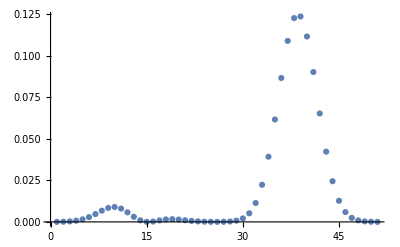

```mathematica
postp=First@Measureθq[zeroMeasurements,{-θopt3},{2}];
ListPlot[postp,PlotRange->All]
```

### Nice Plot

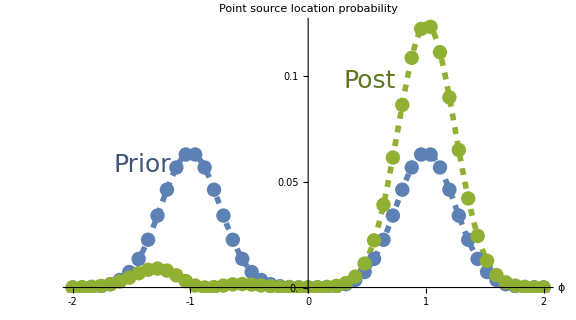

```mathematica
labelStyle=Directive[FontSize->25,FontColor->Black,FontFamily->"Times New Roman",FontSlant->Plain];
ticksStyle=Directive[FontSize->25,FontColor->Black,FontFamily->"Times New Roman",FontSlant->Plain];
axesStyle=Directive[Black];
plotOpts=Sequence[ImageSize->Large,LabelStyle->labelStyle,AxesStyle->axesStyle,TicksStyle->ticksStyle,AspectRatio->1/1.8];

priorColour=RGBColor[0.368417, 0.506779, 0.709798];
postColour = RGBColor[0.560181, 0.691569, 0.194885];

Module[{priorInterp,postInterp,lineThickness,pointSize,linePlot,dotPlot},

priorInterp=Interpolation[Transpose@{ϕList,priorp}];
postInterp=Interpolation[Transpose[{ϕList,postp}]];

lineThickness=0.007;
pointSize=0.018;

linePlot=Plot[
{
Callout[priorInterp[x],Style["Prior",FontColor->Darker@priorColour],{-1.35,0.05},LeaderSize->0,Background->None]
,Callout[postInterp[x],Style["Post",FontColor->Darker@postColour],{0.6,0.09},LeaderSize->0,Background->None]
}
,{x,ϕList[[1]],ϕList[[-1]]},Evaluate@plotOpts
,Ticks->{Range[-2,2,1],Range[0,0.14,0.05]}
,PlotRange->{All,{0,0.125}}
,PlotStyle->{{Thickness[lineThickness],Dashed,priorColour},{Thickness[lineThickness],Dashed,postColour}}
,AxesLabel->{"ϕ","Point source location probability"}
];
dotPlot=ListPlot[
{Transpose@{ϕList,priorp},Transpose@{ϕList,postp}},Evaluate@plotOpts
,PlotStyle->{{priorColour,PointSize[pointSize]},{postColour,PointSize[pointSize]}}
];
pDistPlot=Show[linePlot,dotPlot]
]
```

```mathematica
SetDirectory@NotebookDirectory[];
Export["fig_PDists.png",pDistPlot,ImageResolution->300];
```

## Coherence

```mathematica
θRange = 5.; (* Range of θ displacements to consider *)
nθ = 100; (* θ increment *)
θVals = Range[-θRange,θRange,2θRange/nθ];
```

```mathematica
priorCeList=Quiet@ParallelTable[{θ,Ce[θ,priorp]},{θ,θVals}];
postCeList=Quiet@ParallelTable[{θ,Ce[θ,postp]},{θ,θVals}];
```

General::munfl: 1.27039×10^-157 2.18725×10^-158 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: 1.27039×10^-157 2.18725×10^-158 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: 1.30088×10^-154 2.23974×10^-155 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: 1.30088×10^-154 2.23974×10^-155 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: 1.27039×10^-157 2.18725×10^-158 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: 1.30088×10^-154 2.23974×10^-155 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: 1.30088×10^-154 2.23974×10^-155 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

```mathematica
priorCeInterp=Interpolation[priorCeList];
priorMin=NMinimize[{priorCeInterp[θ],-θRange<θ<θRange},θ];
postCeInterp=Interpolation[postCeList];
postMin=NMinimize[{postCeInterp[θ],-θRange<θ<θRange},θ];

lineThickness = 0.006;
Module[
{coherenceCurvesPlot,thetaPointsPlot,θ3Colour,θ5Colour},

θ3Colour=RGBColor[0.736782672705901, 0.358, 0.5030266573755369];
θ5Colour=RGBColor[0.880722, 0.611041, 0.142051];

coherenceCurvesPlot=Plot[
{
Callout[priorCeInterp[θ],Style["Prior",FontColor->Darker@priorColour],{-2,Above},LeaderSize->0,Background->None],
Callout[postCeInterp[θ],Style["Post",FontColor->Darker@postColour],{2,Above},1.9,LeaderSize->0,Background->None]
},
{θ,-θRange,θRange},
ScalingFunctions->{Identity,Identity},
Evaluate@plotOpts,
Ticks->{Range[-Round@θRange,Round@θRange,2],Range[0,0.5,0.1]},PlotRange->{{-5,5},{0.05,Automatic}},PlotStyle->{{Thickness[lineThickness],priorColour},{Thickness[lineThickness],postColour}},AxesLabel->{"θ","Ensemble coherence vs. measurement basis"},Prolog->{Thickness[lineThickness],Dashed,Lighter@priorColour,Line[{{-θRange,First@priorMin},{θRange,First@priorMin}}],Lighter@postColour,Line[{{-θRange,First@postMin},{θRange,First@postMin}}]},PlotLabel->None];

thetaPointsPlot=ListPlot[
{Callout[{{θopt3,priorCeInterp[θopt3]}},Style["θ_opt1",FontColor->θ3Colour,FontSize->23],{-1.3,0.32}]
,Callout[{{-θopt5,priorCeInterp[θopt5]}},Style["θ_opt2",FontColor->θ5Colour,FontSize->23],{4.5,0.32}]},
PlotStyle->{θ3Colour,θ5Colour}];

coherencePlot=Show[coherenceCurvesPlot,thetaPointsPlot]
]
```

-Graphics-

```mathematica
SetDirectory@NotebookDirectory[];
Export["fig_Coherences.png",coherencePlot,ImageResolution->300];
```